```mathematica
H[a_]:=H0 √(Ωm/a^3)
Ψ[a_]:=-(3 H0^2)/(2 a^3)Ωm
ceff2[a_]:=0
DSolve[a^2 H[a]^2 δa''[a]+(3a H[a]^2+a^2 H[a] H'[a])δa'[a]+(k^2 ceff2[a]/a^2+Ψ[a])δa[a]==0,δa,a]//FullSimplify
```

{{δa→Function[{a},C[1]/a^(3/2)+a C[2]]}}

```mathematica
H[a_]:=H0 √(Ωm/a^3)
Ψ[a_]:=-(3 H0^2)/(2 a^3)Ωm
ceff2[a_]:=cs^2
DSolve[a^2 H[a]^2 δa''[a]+(3a H[a]^2+a^2 H[a] H'[a])δa'[a]+(k^2 ceff2[a]/a^2+Ψ[a])δa[a]==0,δa,a]//FullSimplify
```

{{δa→Function[{a},1/(3 a^(3/2) cs^3 k^3)H0 √Ωm C[1] (-4 a cs^2 k^2 Cos[(2 √a cs k)/(H0 √Ωm)]+3 H0^2 Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+6 √a cs H0 k √Ωm Sin[(2 √a cs k)/(H0 √Ωm)])-1/(32 a^(3/2) cs^3 k^3)15 H0 √Ωm C[2] (6 √a cs H0 k √Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+4 a cs^2 k^2 Sin[(2 √a cs k)/(H0 √Ωm)]-3 H0^2 Ωm Sin[(2 √a cs k)/(H0 √Ωm)])]}}

```mathematica
(* We match to the standard DM growing mode at the start of the cs2 perturbation, ai*)
```

```mathematica
Solve[{(a CC/.a-> ai)==( 1/(3 a^(3/2) cs^3 k^3)H0 √Ωm C[1] (-4 a cs^2 k^2 Cos[(2 √a cs k)/(H0 √Ωm)]+3 H0^2 Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+6 √a cs H0 k √Ωm Sin[(2 √a cs k)/(H0 √Ωm)])-(15 H0 √Ωm C[2] (6 √a cs H0 k √Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+4 a cs^2 k^2 Sin[(2 √a cs k)/(H0 √Ωm)]-3 H0^2 Ωm Sin[(2 √a cs k)/(H0 √Ωm)]))/(32 a^(3/2) cs^3 k^3)/.a-> ai), CC==(D[(H0 √Ωm C[1] (-4 a cs^2 k^2 Cos[(2 √a cs k)/(H0 √Ωm)]+3 H0^2 Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+6 √a cs H0 k √Ωm Sin[(2 √a cs k)/(H0 √Ωm)]))/(3 a^(3/2) cs^3 k^3)-(15 H0 √Ωm C[2] (6 √a cs H0 k √Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+4 a cs^2 k^2 Sin[(2 √a cs k)/(H0 √Ωm)]-3 H0^2 Ωm Sin[(2 √a cs k)/(H0 √Ωm)]))/(32 a^(3/2) cs^3 k^3),a]/.a-> ai)},{C[1],C[2]}]//FullSimplify
```

{{C[1]→-((3 CC (2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+3 H0 √Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)]))/(32 cs^2 H0 k^2 √Ωm)),C[2]→-((CC (3 H0 √Ωm (8 ai cs^2 k^2-5 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)]))/(15 cs^2 H0 k^2 √Ωm))}}

```mathematica
1/(3 a^(3/2) cs^3 k^3)H0 √Ωm C[1] (-4 a cs^2 k^2 Cos[(2 √a cs k)/(H0 √Ωm)]+3 H0^2 Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+6 √a cs H0 k √Ωm Sin[(2 √a cs k)/(H0 √Ωm)])-1/(32 a^(3/2) cs^3 k^3)15 H0 √Ωm C[2] (6 √a cs H0 k √Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+4 a cs^2 k^2 Sin[(2 √a cs k)/(H0 √Ωm)]-3 H0^2 Ωm Sin[(2 √a cs k)/(H0 √Ωm)])/.{C[1]->-1/(32 cs^2 H0 k^2 √Ωm)3 CC (2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+3 H0 √Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)]),C[2]->-((CC (3 H0 √Ωm (8 ai cs^2 k^2-5 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)]))/(15 cs^2 H0 k^2 √Ωm))}//FullSimplify
```

1/(32 a^(3/2) cs^5 k^5)CC ((6 √a cs H0 k √Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+(4 a cs^2 k^2-3 H0^2 Ωm) Sin[(2 √a cs k)/(H0 √Ωm)]) (3 H0 √Ωm (8 ai cs^2 k^2-5 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)])-((-4 a cs^2 k^2+3 H0^2 Ωm) Cos[(2 √a cs k)/(H0 √Ωm)]+6 √a cs H0 k √Ωm Sin[(2 √a cs k)/(H0 √Ωm)]) (2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+3 H0 √Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)]))

```mathematica
(* And then we match the cs2=0 case at a=af *)
```

```mathematica
Solve[{(C[1]/a^(3/2)+a C[2]/.a-> af)==( 1/(32 a^(3/2) cs^5 k^5)CC ((6 √a cs H0 k √Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+(4 a cs^2 k^2-3 H0^2 Ωm) Sin[(2 √a cs k)/(H0 √Ωm)]) (3 H0 √Ωm (8 ai cs^2 k^2-5 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)])-((-4 a cs^2 k^2+3 H0^2 Ωm) Cos[(2 √a cs k)/(H0 √Ωm)]+6 √a cs H0 k √Ωm Sin[(2 √a cs k)/(H0 √Ωm)]) (2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+3 H0 √Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)]))/.a-> af), (D[C[1]/a^(3/2)+a C[2],a]/.a-> af)==(D[1/(32 a^(3/2) cs^5 k^5)CC ((6 √a cs H0 k √Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+(4 a cs^2 k^2-3 H0^2 Ωm) Sin[(2 √a cs k)/(H0 √Ωm)]) (3 H0 √Ωm (8 ai cs^2 k^2-5 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)])-((-4 a cs^2 k^2+3 H0^2 Ωm) Cos[(2 √a cs k)/(H0 √Ωm)]+6 √a cs H0 k √Ωm Sin[(2 √a cs k)/(H0 √Ωm)]) (2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+3 H0 √Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)])),a]/.a-> af)},{C[1],C[2]}]//Simplify
```

{{C[1]→1/(160 cs^5 H0 k^5 √Ωm)CC (-6 (√af-√ai) cs H0 k √Ωm (100 √af √ai cs^2 H0^2 k^2 Ωm+5 H0^2 Ωm (-4 ai cs^2 k^2+15 H0^2 Ωm)+4 af (8 ai cs^4 k^4-5 cs^2 H0^2 k^2 Ωm)) Cos[(2 (√af-√ai) cs k)/(H0 √Ωm)]+(16 af^(3/2) √ai cs^4 k^4 (4 ai cs^2 k^2-15 H0^2 Ωm)-60 √af √ai cs^2 H0^2 k^2 Ωm (4 ai cs^2 k^2-15 H0^2 Ωm)+72 af cs^2 H0^2 k^2 Ωm (8 ai cs^2 k^2-5 H0^2 Ωm)+45 H0^4 Ωm^2 (-8 ai cs^2 k^2+5 H0^2 Ωm)) Sin[(2 (√af-√ai) cs k)/(H0 √Ωm)]),C[2]→1/(40 af^(3/2) cs^3 H0 k^3 √Ωm)CC (2 cs H0 k √Ωm (3 √af (8 ai cs^2 k^2-5 H0^2 Ωm)+√ai (-4 ai cs^2 k^2+15 H0^2 Ωm)) Cos[(2 (√af-√ai) cs k)/(H0 √Ωm)]+(3 H0^2 Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm)+4 √af √ai cs^2 k^2 (-4 ai cs^2 k^2+15 H0^2 Ωm)) Sin[(2 (√af-√ai) cs k)/(H0 √Ωm)])}}

```mathematica
C[1]/a^(3/2)+a C[2]/.{C[1]->1/(160 cs^5 H0 k^5 √Ωm)CC (-6 (√af-√ai) cs H0 k √Ωm (100 √af √ai cs^2 H0^2 k^2 Ωm+5 H0^2 Ωm (-4 ai cs^2 k^2+15 H0^2 Ωm)+4 af (8 ai cs^4 k^4-5 cs^2 H0^2 k^2 Ωm)) Cos[(2 (√af-√ai) cs k)/(H0 √Ωm)]+(16 af^(3/2) √ai cs^4 k^4 (4 ai cs^2 k^2-15 H0^2 Ωm)-60 √af √ai cs^2 H0^2 k^2 Ωm (4 ai cs^2 k^2-15 H0^2 Ωm)+72 af cs^2 H0^2 k^2 Ωm (8 ai cs^2 k^2-5 H0^2 Ωm)+45 H0^4 Ωm^2 (-8 ai cs^2 k^2+5 H0^2 Ωm)) Sin[(2 (√af-√ai) cs k)/(H0 √Ωm)]),C[2]->1/(40 af^(3/2) cs^3 H0 k^3 √Ωm)CC (2 cs H0 k √Ωm (3 √af (8 ai cs^2 k^2-5 H0^2 Ωm)+√ai (-4 ai cs^2 k^2+15 H0^2 Ωm)) Cos[(2 (√af-√ai) cs k)/(H0 √Ωm)]+(3 H0^2 Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm)+4 √af √ai cs^2 k^2 (-4 ai cs^2 k^2+15 H0^2 Ωm)) Sin[(2 (√af-√ai) cs k)/(H0 √Ωm)])}//Simplify
```

1/(160 a^(3/2) cs^5 H0 k^5 √Ωm)CC (-6 (√af-√ai) cs H0 k √Ωm (100 √af √ai cs^2 H0^2 k^2 Ωm+5 H0^2 Ωm (-4 ai cs^2 k^2+15 H0^2 Ωm)+4 af (8 ai cs^4 k^4-5 cs^2 H0^2 k^2 Ωm)) Cos[(2 (√af-√ai) cs k)/(H0 √Ωm)]+(16 af^(3/2) √ai cs^4 k^4 (4 ai cs^2 k^2-15 H0^2 Ωm)-60 √af √ai cs^2 H0^2 k^2 Ωm (4 ai cs^2 k^2-15 H0^2 Ωm)+72 af cs^2 H0^2 k^2 Ωm (8 ai cs^2 k^2-5 H0^2 Ωm)+45 H0^4 Ωm^2 (-8 ai cs^2 k^2+5 H0^2 Ωm)) Sin[(2 (√af-√ai) cs k)/(H0 √Ωm)]+1/af^(3/2)4 a^(5/2) cs^2 k^2 (2 cs H0 k √Ωm (3 √af (8 ai cs^2 k^2-5 H0^2 Ωm)+√ai (-4 ai cs^2 k^2+15 H0^2 Ωm)) Cos[(2 (√af-√ai) cs k)/(H0 √Ωm)]+(3 H0^2 Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm)+4 √af √ai cs^2 k^2 (-4 ai cs^2 k^2+15 H0^2 Ωm)) Sin[(2 (√af-√ai) cs k)/(H0 √Ωm)]))

```mathematica
(* Here is the full gdm evolution *)
Clear[h,H0,Ωm,k,ai,af]
h=0.7;
H0=0.0003335 h;
Ωm=1;
k=0.00528;
ai=0.01489;
af=0.020;
da = Log[af/ai]; 
cs2want=0.0001
cs=√(cs2want/da);
CC=1;
δgdm[a_]:=Piecewise[{{CC a,a<ai},{1/(32 a^(3/2) cs^5 k^5)CC ((6 √a cs H0 k √Ωm Cos[(2 √a cs k)/(H0 √Ωm)]+(4 a cs^2 k^2-3 H0^2 Ωm) Sin[(2 √a cs k)/(H0 √Ωm)]) (3 H0 √Ωm (8 ai cs^2 k^2-5 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)])-((-4 a cs^2 k^2+3 H0^2 Ωm) Cos[(2 √a cs k)/(H0 √Ωm)]+6 √a cs H0 k √Ωm Sin[(2 √a cs k)/(H0 √Ωm)]) (2 √ai cs k (4 ai cs^2 k^2-15 H0^2 Ωm) Cos[(2 √ai cs k)/(H0 √Ωm)]+3 H0 √Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm) Sin[(2 √ai cs k)/(H0 √Ωm)])),ai≤ a≤ af}},1/(160 a^(3/2) cs^5 H0 k^5 √Ωm)CC (-6 (√af-√ai) cs H0 k √Ωm (100 √af √ai cs^2 H0^2 k^2 Ωm+5 H0^2 Ωm (-4 ai cs^2 k^2+15 H0^2 Ωm)+4 af (8 ai cs^4 k^4-5 cs^2 H0^2 k^2 Ωm)) Cos[(2 (√af-√ai) cs k)/(H0 √Ωm)]+(16 af^(3/2) √ai cs^4 k^4 (4 ai cs^2 k^2-15 H0^2 Ωm)-60 √af √ai cs^2 H0^2 k^2 Ωm (4 ai cs^2 k^2-15 H0^2 Ωm)+72 af cs^2 H0^2 k^2 Ωm (8 ai cs^2 k^2-5 H0^2 Ωm)+45 H0^4 Ωm^2 (-8 ai cs^2 k^2+5 H0^2 Ωm)) Sin[(2 (√af-√ai) cs k)/(H0 √Ωm)]+1/af^(3/2)4 a^(5/2) cs^2 k^2 (2 cs H0 k √Ωm (3 √af (8 ai cs^2 k^2-5 H0^2 Ωm)+√ai (-4 ai cs^2 k^2+15 H0^2 Ωm)) Cos[(2 (√af-√ai) cs k)/(H0 √Ωm)]+(3 H0^2 Ωm (-8 ai cs^2 k^2+5 H0^2 Ωm)+4 √af √ai cs^2 k^2 (-4 ai cs^2 k^2+15 H0^2 Ωm)) Sin[(2 (√af-√ai) cs k)/(H0 √Ωm)]))]
```

0.0001

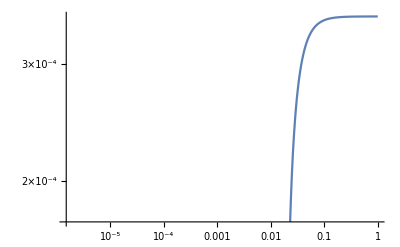

```mathematica
LogLogPlot[{(CC a-δgdm[a])/(CC a )},{a,0.0001*ai,1}]
```

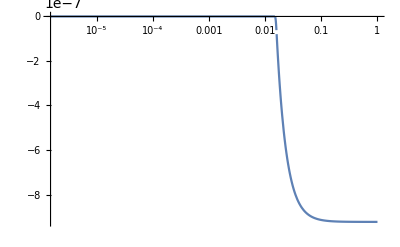

```mathematica
LogLinearPlot[(-δgdm[a]*Ψ[a]*a^2+CC*a*Ψ[a]*a^2)/k^2,{a,0.0001* ai,1}]
```

```mathematica
3
```

```mathematica
dgdm[0]
```

dgdm[0]

```mathematica
f[a_]:=-(CC a-δgdm[a])/(CC a )
```

```mathematica
Exp[3]

g[a_]:=-f[a]
```

ⅇ^3

```mathematica
lg[a_]:=Log[g[a]]
```

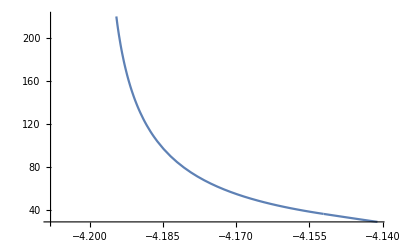

```mathematica
Plot[(lg[Exp[x+0.01]]-lg[Exp[x-.01]])/0.02,{x,Log[ai]-0.001,Log[af]+0.001}]
```